```mathematica
DataE = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_three.csv"];
```

```mathematica
DataSHLV = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_HLV.csv"];
```

```mathematica
DataSHLVK = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_HLVK.csv"];
```

```mathematica
DataSHLVKI = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_HLVKI.csv"];
```

```mathematica
SinterpHLV = Interpolation[DataSHLV];
```

```mathematica
SinterpHLVK = Interpolation[DataSHLVK];
```

```mathematica
SinterpHLVKI = Interpolation[DataSHLVKI];
```

```mathematica
Einterp = Interpolation[DataE];
```

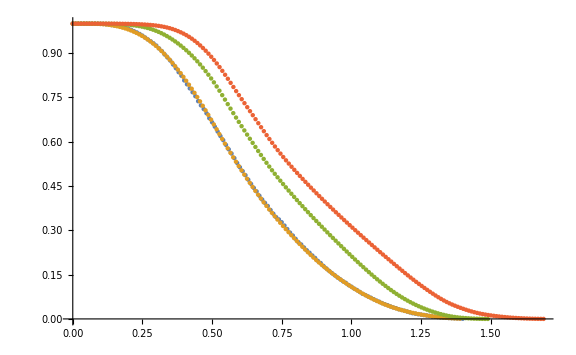

```mathematica
ListPlot[{DataE,DataSHLV,DataSHLVK,DataSHLVKI},ImageSize->Large]
```

```mathematica
Residual = Table[ {x,(Einterp[x]- Sinterp[x])/Einterp[x]},{i,1,Length[DataE]}];
```

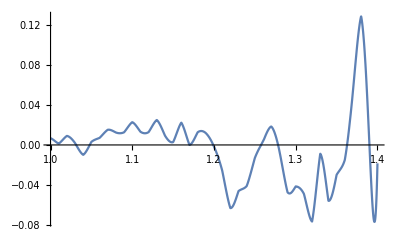

```mathematica
Plot[2(Einterp[x]- Sinterp[x])/(Einterp[x]+Sinterp[x]),{x,1,1.4},PlotRange->Full]
```

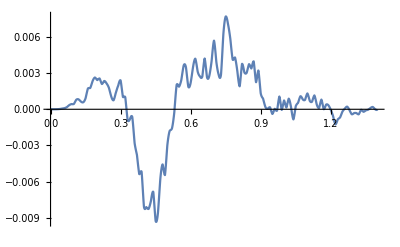

```mathematica
Plot[{(Einterp[x]- SinterpHLV[x])},{x,0,1.4},PlotRange->Full,ImageSize->Full]
```